## 6.859 A4: Does Charlie WFH?

## Georgios Varnavides, Max L’Etoille

## 2010 Census Tracts

### Shapefiles

```mathematica
SetDirectory[FileNameDrop[NotebookDirectory[],-2]]
```

/home/george/Documents/git-repos/a4-does-charlie-wfh

```mathematica
censusTracts["Middlesex"]=Association[Import["data/tl_2010_25017_tract10.zip","Data"][[1]]];
censusTracts["Norfolk"]=Association[Import["data/tl_2010_25021_tract10.zip","Data"][[1]]];
censusTracts["Suffolk"]=Association[Import["data/tl_2010_25025_tract10.zip","Data"][[1]]];
```

```mathematica
GeoGraphics[{
EdgeForm[Black],FaceForm[None],
censusTracts["Middlesex"]["Geometry"],
Delete[censusTracts["Norfolk"]["Geometry"],85],
Delete[censusTracts["Suffolk"]["Geometry"],56]
}]
```

-Graphics-

```mathematica
censusTractsPolygonsAsc=KeyDrop[KeyMap[ToExpression,Join@@Table[AssociationThread[Association[censusTracts[county]["LabeledData"]]["TRACTCE10"]->censusTracts[county]["Geometry"]],{county,{"Middlesex","Norfolk","Suffolk"}}]],{990101,423100}];
```

### Neighborhood Covariates

```mathematica
data=Import["data/tract_covariates.csv","Data"];
data=Select[data,#[[1]]==25&&(#[[2]]==17||#[[2]]==21||#[[2]]==25)&];
```

```mathematica
Import["data/tract_covariates.csv",{"Data",1}]
```

{state,county,tract,cz,czname,hhinc_mean2000,mean_commutetime2000,frac_coll_plus2000,frac_coll_plus2010,foreign_share2010,med_hhinc1990,med_hhinc2016,popdensity2000,poor_share2010,poor_share2000,poor_share1990,share_white2010,share_black2010,share_hisp2010,share_asian2010,share_black2000,share_white2000,share_hisp2000,share_asian2000,gsmn_math_g3_2013,rent_twobed2015,singleparent_share2010,singleparent_share1990,singleparent_share2000,traveltime15_2010,emp2000,mail_return_rate2010,ln_wage_growth_hs_grad,jobs_total_5mi_2015,jobs_highpay_5mi_2015,popdensity2010,ann_avg_job_growth_2004_2013,job_density_2013}

```mathematica
Block[{
cf=ResourceFunction["ColorBrewerData"]["BrBG","ColorFunction"],
mbtaLines,
medianHouseholdIncome
},

medianHouseholdIncome=DeleteCases[Thread[Lookup[censusTractsPolygonsAsc,data[[All,3]],FilledCurve[]]->data[[All,12]]]/.""->Missing[],_FilledCurve->_];

(*likely requires evaluating mbta-shapefiles.nb*)
mbtaLines=GeoGraphics[{
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}],MapThread[{PointSize[Large],#1,Point[cleanedUpStationsByLine[#2][[All,3]]]}&,{cleanedUpCols,cleanedUpStationsByLine//Keys}]},GeoBackground->None];

GeoRegionValuePlot[medianHouseholdIncome,MissingStyle->HatchFilling[π/4,0.5,2.5],GeoBackground->None,ColorFunction->cf,PlotLegends->Automatic,ColorFunctionBinning->24,LabelStyle->16,ImageSize->500,Epilog->mbtaLines[[1,1]],(*GeoRange*)mbtaLines[[10]]]//Quiet]
```

-Graphics-

### Tracts By Line

```mathematica
censusTractsRegionMembers=RegionMember[Polygon[First[#]["LatitudeLongitude"]]]&/@KeyDrop[censusTractsPolygonsAsc,980101];
```

```mathematica
lineGraphics=Map[#/.Line[x_]:>GeoPosition[x]["LatitudeLongitude"]&,(geometryAssociations["MBTA_ARC"][[#]]&/@cleanedUpRoutesByLine)];
```

```mathematica
tractsCrossingLine[col_]:=tractsCrossingLine[col]=Union[Flatten[Table[Position[Or@@@Through[Values[censusTractsRegionMembers][If[ArrayDepth[l]==2,l,Join@@l]]],True],{l,lineGraphics[col]}] ]]
```

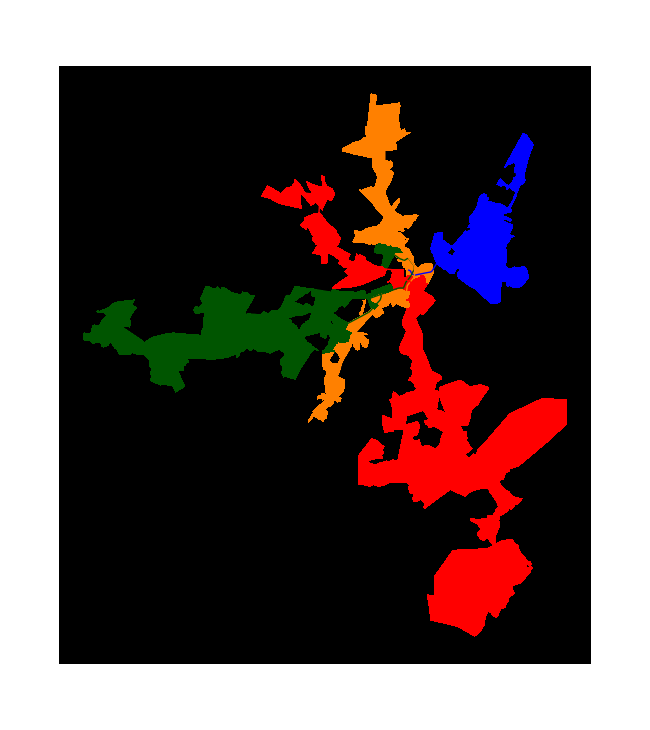
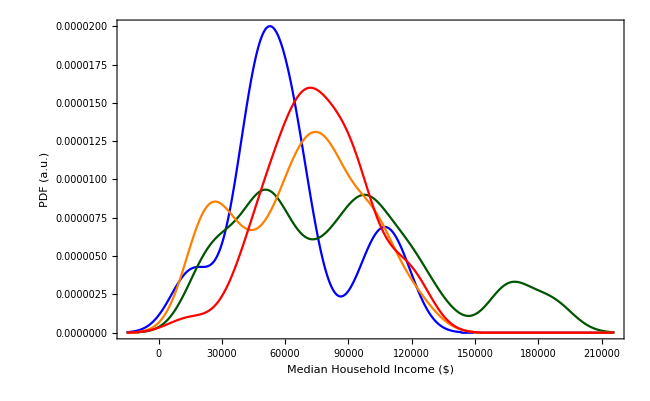

```mathematica
Row[{
GeoGraphics[
{Thread[{cleanedUpCols,Lookup[censusTractsPolygonsAsc,Keys[KeyDrop[censusTractsPolygonsAsc,980101]][[tractsCrossingLine[#]]]]&/@Keys[lineGraphics]}],
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}]},GeoBackground->None,ImageSize->650],SmoothHistogram[DeleteCases[Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Keys[KeyDrop[censusTractsPolygonsAsc,980101]][[tractsCrossingLine[#]]]]&/@Keys[lineGraphics],"",{2}],10000,PlotStyle->cleanedUpCols,Frame->True,ImageSize->650,FrameLabel->{"Median Household Income ($)","PDF (a.u.)"},BaseStyle->18]}]
```